```mathematica
$N = 5; $K = 5;α=1.6;
mat  = Partition[(#-1/($N)Tr[#]IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[1/(√($N α)), $N], 100000*$K], $K];
```

```mathematica
rad = Chop@Total[Map[Tr[#.#]&, mat, {2}], {2}];
```

```mathematica
($K(($N)^2-1))/($N)1/Mean[rad]
```

1.60027

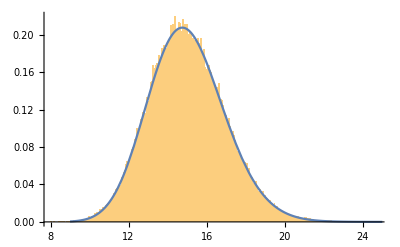

```mathematica
Show[
Histogram[rad, 400, PDF],
Plot[PDF[GammaDistribution[$K*(($N)^2-1)/2, 2/(α $N)], x], {x, 9, 25}]
]
```